```mathematica
Cos[40](1+Sqrt[3]Tan[90])//FullSimplify
```

Cos[40] (1+√3 Tan[90])

```mathematica
123*145
```

17835

```mathematica
IntegerDigits/@{123,456,123*456}
```

{{1,2,3},{4,5,6},{5,6,0,8,8}}

```mathematica
并
```

```mathematica
a=Sort/@Flatten[Table[{i,j},{j,1,#},{i,j+1,#}],1]&;
q[{a_,b_}]:=Nor[Count[Differences[Sort@Flatten[IntegerDigits/@{a,b,a*b},1]],0]>0];
data=Select[a[1000],q]
```

{{2,3},{2,4},{2,5},{2,7},{2,8},{2,9},{2,15},{2,17},{2,18},{2,19},{2,34},{2,35},{2,38},{2,39},{2,43},{2,45},{2,48},{2,53},{2,54},{2,65},{2,67},{2,69},{2,73},{2,78},{2,79},{2,85},{2,93},{2,154},{2,178},{2,179},{2,185},{2,307},{2,309},{2,345},{2,354},{2,358},{2,359},{2,415},{2,435},{2,453},{2,458},{2,465},{2,478},{2,485},{2,534},{2,538},{2,539},{2,543},{2,548},{2,654},{2,679},{2,685},{2,769},{2,793},{2,835},{2,845},{2,853},{2,865},{2,935},{3,4},{3,6},{3,7},{3,8},{3,9},{3,16},{3,18},{3,19},{3,26},{3,27},{3,29},{3,54},{3,58},{3,64},{3,67},{3,68},{3,69},{3,87},{3,89},{3,168},{3,169},{3,176},{3,182},{3,189},{3,192},{3,194},{3,218},{3,219},{3,267},{3,269},{3,568},{3,582},{3,594},{3,609},{3,658},{3,819},{3,906},{3,916},{3,918},{4,5},{4,7},{4,8},{4,9},{4,13},{4,15},{4,17},{4,18},{4,19},{4,27},{4,38},{4,39},{4,59},{4,78},{4,79},{4,89},{4,92},{4,95},{4,127},{4,152},{4,157},{4,158},{4,173},{4,189},{4,192},{4,195},{4,209},{4,215},{4,219},{4,259},{4,392},{4,517},{4,519},{4,579},{4,695},{4,709},{4,715},{4,789},{4,792},{4,795},{4,815},{4,819},{4,879},{4,907},{4,918},{5,6},{5,8},{5,12},{5,14},{5,16},{5,18},{5,26},{5,28},{5,32},{5,34},{5,36},{5,38},{5,46},{5,62},{5,64},{5,68},{5,72},{5,76},{5,78},{5,82},{5,86},{5,92},{5,96},{5,128},{5,134},{5,138},{5,146},{5,164},{5,172},{5,184},{5,186},{5,268},{5,276},{5,278},{5,286},{5,296},{5,328},{5,364},{5,372},{5,384},{5,436},{5,438},{5,476},{5,478},{5,628},{5,682},{5,728},{5,762},{5,764},{5,782},{5,784},{5,826},{5,832},{5,862},{5,872},{5,962},{5,972},{6,7},{6,9},{6,13},{6,15},{6,29},{6,35},{6,43},{6,45},{6,57},{6,89},{6,97},{6,145},{6,157},{6,289},{6,293},{6,307},{6,309},{6,453},{6,485},{6,529},{6,703},{6,715},{6,817},{6,903},{6,913},{7,8},{7,9},{7,12},{7,14},{7,24},{7,28},{7,52},{7,56},{7,58},{7,59},{7,69},{7,89},{7,93},{7,94},{7,136},{7,208},{7,209},{7,308},{7,409},{7,456},{7,458},{7,586},{7,589},{7,693},{7,802},{7,803},{7,843},{7,859},{7,893},{7,902},{7,904},{7,912},{8,9},{8,12},{8,37},{8,45},{8,52},{8,59},{8,63},{8,64},{8,74},{8,79},{8,92},{8,94},{8,95},{8,245},{8,307},{8,345},{8,407},{8,459},{8,465},{8,469},{8,512},{8,537},{8,579},{8,592},{8,615},{8,634},{8,674},{8,679},{8,703},{8,704},{8,742},{8,753},{8,754},{8,794},{8,915},{8,932},{8,942},{8,953},{8,954},{9,42},{9,52},{9,72},{9,84},{9,204},{9,206},{9,207},{9,306},{9,402},{9,408},{9,412},{9,418},{9,512},{9,602},{9,603},{9,608},{9,638},{9,647},{9,702},{9,712},{9,804},{9,806},{9,814},{9,834},{9,836},{12,38},{12,39},{12,48},{12,57},{12,59},{12,65},{12,67},{12,78},{12,483},{12,695},{13,46},{13,54},{13,56},{13,74},{13,406},{13,546},{13,604},{13,754},{14,59},{14,67},{14,68},{15,24},{15,26},{15,32},{15,42},{15,48},{15,62},{15,326},{15,486},{15,492},{15,632},{15,648},{16,37},{16,45},{18,32},{18,39},{18,42},{18,52},{18,54},{18,297},{18,392},{18,409},{19,32},{19,204},{19,253},{19,402},{19,453},{23,46},{23,69},{23,196},{24,57},{26,35},{26,345},{27,34},{27,198},{27,594},{28,157},{32,49},{32,169},{34,52},{34,58},{34,178},{34,185},{36,495},{37,58},{38,42},{38,52},{38,65},{38,159},{39,54},{39,56},{39,186},{39,402},{42,138},{45,82},{45,396},{46,85},{46,715},{48,65},{48,159},{48,165},{52,79},{52,367},{53,76},{53,92},{54,168},{54,297},{57,86},{58,64},{59,68},{59,78},{59,108},{59,136},{62,87},{63,154},{63,927},{68,74},{69,108},{72,95},{74,85},{78,345}}

```mathematica
Transpose@{{2,3},{2,4},{2,5},{2,7},{2,8},{2,9},{2,15},{2,17},{2,18},{2,19},{2,34},{2,35},{2,38},{2,39},{2,43},{2,45},{2,48},{2,53},{2,54},{2,65},{2,67},{2,69},{2,73},{2,78},{2,79}}//Last
```

{3,4,5,7,8,9,15,17,18,19,34,35,38,39,43,45,48,53,54,65,67,69,73,78,79}

```mathematica
Integrate[1/(a + b Cos[x])^2,x]
```

(2 a ArcTanh[((a-b) Tan[x/2])/(√(-a^2+b^2))])/((-a^2+b^2)^(3/2))-(b Sin[x])/((a-b) (a+b) (a+b Cos[x]))

```mathematica
12345679*4
```

49382716

```mathematica
x==y Cot[Pi y/2]/.y->Cos[xi/n]
```

x==Cos[xi/n] Cot[1/2 π Cos[xi/n]]

```mathematica
Quit
```

```mathematica
eq=(Area@SSSTriangle[p,x,p+2k p/x])==(x Sqrt[p^2-(k/2)^2]/2)/.p->Sqrt[2];
First@Solve[{eq},x]
```

{x→2 k^(1/3)}

```mathematica
Quit
```

```mathematica
((2 p+(2 k p)/x-x) (-(2 k p)/x+x) ((2 k p)/x+x) (2 p+(2 k p)/x+x))==(4 p^2-k^2) x^2
```

```mathematica
内积
```

```mathematica
Sin[2Pi/7]//RootReduce//ToRadicals
```

√(7/12-7^(2/3)/(12 2^(2/3) (-1+3 ⅈ √3)^(1/3))+(ⅈ 7^(2/3))/(4 2^(2/3) √3 (-1+3 ⅈ √3)^(1/3))-1/24 (7/2 (-1+3 ⅈ √3))^(1/3)-(ⅈ (7/2 (-1+3 ⅈ √3))^(1/3))/(8 √3))

```mathematica
ToRadicals[Cos[(3 π)/14]]
```

-1/2 (-1)^(11/14) (1+(-1)^(3/7))

```mathematica
Array[{#,FactorInteger[#],RootReduce@Cos[2Pi/#]}&,24]//TableForm
```

1 | 1 | 1 | 1
2 | 2 | 1 | -1
3 | 3 | 1 | -1/2
4 | 2 | 2 | 0
5 | 5 | 1 | 1/4 (-1+√5)
6 | 2 | 1
3 | 1 | 1/2
7 | 7 | 1 | Root[-1-4 #1+4 #1^2+8 #1^3&,3]
8 | 2 | 3 | 1/(√2)
9 | 3 | 2 | Root[1-6 #1+8 #1^3&,3]
10 | 2 | 1
5 | 1 | 1/4 (1+√5)
11 | 11 | 1 | Root[1+6 #1-12 #1^2-32 #1^3+16 #1^4+32 #1^5&,5]
12 | 2 | 2
3 | 1 | (√3)/2
13 | 13 | 1 | Root[-1+6 #1+24 #1^2-32 #1^3-80 #1^4+32 #1^5+64 #1^6&,6]
14 | 2 | 1
7 | 1 | Root[1-4 #1-4 #1^2+8 #1^3&,3]
15 | 3 | 1
5 | 1 | Root[1+8 #1-16 #1^2-8 #1^3+16 #1^4&,4]
16 | 2 | 4 | Root[1-8 #1^2+8 #1^4&,4]
17 | 17 | 1 | Root[1-8 #1-40 #1^2+80 #1^3+240 #1^4-192 #1^5-448 #1^6+128 #1^7+256 #1^8&,8]
18 | 2 | 1
3 | 2 | Root[-1-6 #1+8 #1^3&,3]
19 | 19 | 1 | Root[1+10 #1-40 #1^2-160 #1^3+240 #1^4+672 #1^5-448 #1^6-1024 #1^7+256 #1^8+512 #1^9&,9]
20 | 2 | 2
5 | 1 | Root[5-20 #1^2+16 #1^4&,4]
21 | 3 | 1
7 | 1 | Root[1-16 #1+32 #1^2+48 #1^3-96 #1^4-32 #1^5+64 #1^6&,6]
22 | 2 | 1
11 | 1 | Root[-1+6 #1+12 #1^2-32 #1^3-16 #1^4+32 #1^5&,5]
23 | 23 | 1 | Root[-1-12 #1+60 #1^2+280 #1^3-560 #1^4-1792 #1^5+1792 #1^6+4608 #1^7-2304 #1^8-5120 #1^9+1024 #1^10+2048 #1^11&,11]
24 | 2 | 3
3 | 1 | Root[1-16 #1^2+16 #1^4&,4]

```mathematica
Table[{p,AlgebraicNumberPolynomial[ToNumberField@Cos[2Pi/p],x]},{p,Prime[Range[10]]}]//TableForm
```

2 | -1
3 | -1/2
5 | -1/4+x/4
7 | x^2/2-x^5/2
11 | x^2/2-x^9/2
13 | x^2/2-x^11/2
17 | x^2/2-x^15/2
19 | x^2/2-x^17/2
23 | x^2/2-x^21/2
29 | x^2/2-x^27/2

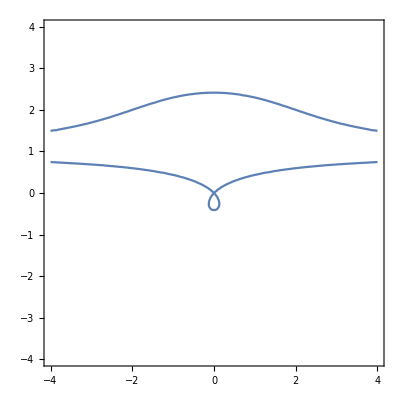

```mathematica
ContourPlot[{(x^2+y^2)(y-1)^2==2y^2,(x^2+y^2)(y-1)^2==-2y^2},{x,-4,4},{y,-4,4}]
```

```mathematica
{
```

```mathematica
Eliminate[{p y+q x+r==0,a x^2+b y^2+c x y+d x+e y+f==0},y]
```

b r^2+r (-e p-c p x+2 b q x)==-f p^2-d p^2 x+e p q x-a p^2 x^2+c p q x^2-b q^2 x^2

```mathematica
Solve[b r^2+r (-e p-c p x+2 b q x)==-f p^2-d p^2 x+e p q x-a p^2 x^2+c p q x^2-b q^2 x^2,{x}]
```

{{x→(-d p^2+e p q+c p r-2 b q r-√((d p^2-e p q-c p r+2 b q r)^2-4 (a p^2-c p q+b q^2) (f p^2-e p r+b r^2)))/(2 (a p^2-c p q+b q^2))},{x→(-d p^2+e p q+c p r-2 b q r+√((d p^2-e p q-c p r+2 b q r)^2-4 (a p^2-c p q+b q^2) (f p^2-e p r+b r^2)))/(2 (a p^2-c p q+b q^2))}}

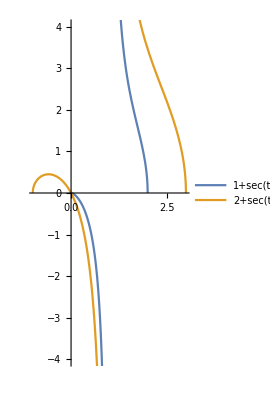

```mathematica
PolarPlot[Evaluate@Array[#+Sec[t]&,2],{t,0,Pi},Exclusions->Cos[t]==0,PlotLegends->"Expressions",PlotRange->{-4,4}]
```

```mathematica
Integrate[Sec[t]^2+k (Cos[t]+k Sin[t]^2),{t,ArcCos[-1/k],π}]
```

1/4 k^2 (π+2 Arg[-ⅈ+√(-1+k^2)]+Sin[2 Arg[-ⅈ+√(-1+k^2)]])

{-√(-1+k^2)+(k^2 π)/2-k^2 ArcCot[√(-1+k^2)],√(-1+k^2)-2 k ArcCosh[k]+k^2 ArcSec[k]}

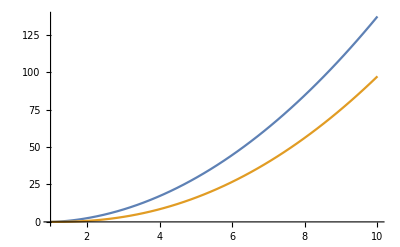

```mathematica
Expand[2{1/4 (-2 √(-1+k^2)+k^2 π-2 k^2 ArcCot[√(-1+k^2)]),1/2 (√(-1+k^2)-2 k ArcCosh[k]+k^2 ArcSec[k])}]
Plot[%,{k,1,10}]
```

```mathematica
ArcCos[-1/k]//FullSimplify
```

ArcSec[-k]

```mathematica
FullSimplify[1/4 k^2 (π-2 ⅈ Log[(-ⅈ+√(-1+k^2))/k]-ⅈ Sinh[2 Log[(-ⅈ+√(-1+k^2))/k]])//TrigToExp//ExpandAll,k>1]
```

-1/2 √(-1+k^2)+(k^2 π)/4-1/2 k^2 ArcCot[√(-1+k^2)]

```mathematica
TrigToExp[1/4 (-2 √(-1+k^2)+k^2 π-2 k^2 ArcCot[√(-1+k^2)])]//
```

1/4 (-2 √(-1+k^2)+k^2 π-2 k^2 ArcCot[√(-1+k^2)])

```mathematica
ArcCos[x]//TrigToExp
```

π/2+ⅈ Log[ⅈ x+√(1-x^2)]

```mathematica
FullSimplify[ⅈ  Log[(-ⅈ+√(-1+k^2))/k]//ComplexExpand,k>1]
```

-Arg[-ⅈ+√(-1+k^2)]

```mathematica
FullSimplify@Table[{-Arg[-ⅈ+√(-1+k^2)],},{k,1,20}]
```

{{π/2,π/2},{π/6,π/6},{ArcCot[2 √2],ArcCot[2 √2]},{ArcCot[√15],ArcCot[√15]},{ArcCot[2 √6],ArcCot[2 √6]},{ArcCot[√35],ArcCot[√35]},{ArcCot[4 √3],ArcCot[4 √3]},{ArcCot[3 √7],ArcCot[3 √7]},{ArcCot[4 √5],ArcCot[4 √5]},{ArcCot[3 √11],ArcCot[3 √11]},{ArcCot[2 √30],ArcCot[2 √30]},{ArcCot[√143],ArcCot[√143]},{ArcCot[2 √42],ArcCot[2 √42]},{ArcCot[√195],ArcCot[√195]},{ArcCot[4 √14],ArcCot[4 √14]},{ArcCot[√255],ArcCot[√255]},{ArcCot[12 √2],ArcCot[12 √2]},{ArcCot[√323],ArcCot[√323]},{ArcCot[6 √10],ArcCot[6 √10]},{ArcCot[√399],ArcCot[√399]}}

```mathematica
-√(-1+k^2)+(k^2 π)/2-k^2 ArcCot[√(-1+k^2)]
```

```mathematica
eq=Thread[{x0+t Cos[xi],t Sin[xi]}=={Cos[af],Sin[af]}]
ans={Cos[af],Sin[af]}/.Solve[{Eliminate[eq,t]},af]
```

{x0+t Cos[xi]==Cos[af],t Sin[xi]==Sin[af]}

{{ConditionalExpression[Cos[ArcTan[(x0 Sin[xi]^2-√(Cos[xi]^4+Cos[xi]^2 Sin[xi]^2-x0^2 Cos[xi]^2 Sin[xi]^2))/(Cos[xi]^2+Sin[xi]^2),Sec[xi] (-x0 Sin[xi]+(x0 Sin[xi]^3)/(Cos[xi]^2+Sin[xi]^2)-(Sin[xi] √(-Cos[xi]^2 (-Cos[xi]^2-Sin[xi]^2+x0^2 Sin[xi]^2)))/(Cos[xi]^2+Sin[xi]^2))]+2 π C[1]],C[1]∈Integers],ConditionalExpression[Sin[ArcTan[(x0 Sin[xi]^2-√(Cos[xi]^4+Cos[xi]^2 Sin[xi]^2-x0^2 Cos[xi]^2 Sin[xi]^2))/(Cos[xi]^2+Sin[xi]^2),Sec[xi] (-x0 Sin[xi]+(x0 Sin[xi]^3)/(Cos[xi]^2+Sin[xi]^2)-(Sin[xi] √(-Cos[xi]^2 (-Cos[xi]^2-Sin[xi]^2+x0^2 Sin[xi]^2)))/(Cos[xi]^2+Sin[xi]^2))]+2 π C[1]],C[1]∈Integers]},{ConditionalExpression[Cos[ArcTan[(x0 Sin[xi]^2+√(Cos[xi]^4+Cos[xi]^2 Sin[xi]^2-x0^2 Cos[xi]^2 Sin[xi]^2))/(Cos[xi]^2+Sin[xi]^2),Sec[xi] (-x0 Sin[xi]+(x0 Sin[xi]^3)/(Cos[xi]^2+Sin[xi]^2)+(Sin[xi] √(-Cos[xi]^2 (-Cos[xi]^2-Sin[xi]^2+x0^2 Sin[xi]^2)))/(Cos[xi]^2+Sin[xi]^2))]+2 π C[1]],C[1]∈Integers],ConditionalExpression[Sin[ArcTan[(x0 Sin[xi]^2+√(Cos[xi]^4+Cos[xi]^2 Sin[xi]^2-x0^2 Cos[xi]^2 Sin[xi]^2))/(Cos[xi]^2+Sin[xi]^2),Sec[xi] (-x0 Sin[xi]+(x0 Sin[xi]^3)/(Cos[xi]^2+Sin[xi]^2)+(Sin[xi] √(-Cos[xi]^2 (-Cos[xi]^2-Sin[xi]^2+x0^2 Sin[xi]^2)))/(Cos[xi]^2+Sin[xi]^2))]+2 π C[1]],C[1]∈Integers]}}

```mathematica
pos1=FullSimplify[{x0 Sin[xi]^2-Cos[xi] √(1-x0^2 Sin[xi]^2),-Cos[xi] Sin[xi] (x0+√(1-(-1+x0^2) Tan[xi]^2))},0<xi<2Pi]//ExpandAll
pos2=FullSimplify[{x0 Sin[xi]^2+Cos[xi] √(1-x0^2 Sin[xi]^2),Cos[xi] Sin[xi] (-x0+√(1-(-1+x0^2) Tan[xi]^2))},0<xi<2Pi]//ExpandAll
```

{x0 Sin[xi]^2-Cos[xi] √(1-x0^2 Sin[xi]^2),-x0 Cos[xi] Sin[xi]-Cos[xi] Sin[xi] √(1+Tan[xi]^2-x0^2 Tan[xi]^2)}

{x0 Sin[xi]^2+Cos[xi] √(1-x0^2 Sin[xi]^2),-x0 Cos[xi] Sin[xi]+Cos[xi] Sin[xi] √(1+Tan[xi]^2-x0^2 Tan[xi]^2)}

```mathematica
tce1=FullSimplify[pos1+{d Cos[xi],d Sin[xi]}/.{x0->-0},0<xi<2Pi]~Join~{d}
tce2=FullSimplify[pos2+{d Cos[xi],d Sin[xi]}/.{x0->-0},0<xi<2Pi]~Join~{d}
ParametricPlot3D[{tce1,tce2},{xi,0,2Pi},{d,0,4},PlotPoints->25,MaxRecursion->2]
```

{(-1+d) Cos[xi],(d-Abs[Sec[xi]] Cos[xi]) Sin[xi],d}

{(1+d) Cos[xi],(d+Abs[Sec[xi]] Cos[xi]) Sin[xi],d}

-Graphics3D-

{x==d Cos[xi]+x0 Sin[xi]^2-Cos[xi] √(1-x0^2 Sin[xi]^2),y==d Sin[xi]-x0 Cos[xi] Sin[xi]-Cos[xi] Sin[xi] √(1+Tan[xi]^2-x0^2 Tan[xi]^2)}

```mathematica
Eliminate[Thread[{x,y}==pos1+{d Cos[xi],d Sin[xi]}],xi].
```

$Aborted

Csc[α-θ] Sin[α] ρ_0==1

```mathematica
Solve[{Subscript[ρ,0] Sin[α]/Sin[α-θ]==1},α][[{1,2}]]//FullSimplify
eq=FullSimplify[Subscript[ρ,0] Sin[α]/Sin[α-θ]/.%]//Union
```

{{α→-ArcCos[(-Cos[θ]+ρ_0)/(√(1-2 Cos[θ] ρ_0+ρ_0^2))]},{α→ArcCos[(-Cos[θ]+ρ_0)/(√(1-2 Cos[θ] ρ_0+ρ_0^2))]}}

{Csc[θ+ArcCos[(-Cos[θ]+ρ_0)/(√(1-2 Cos[θ] ρ_0+ρ_0^2))]] ρ_0 √(Sin[θ]^2/(1-2 Cos[θ] ρ_0+ρ_0^2)),Sec[θ+ArcSin[(-Cos[θ]+ρ_0)/(√(1-2 Cos[θ] ρ_0+ρ_0^2))]] ρ_0 √(Sin[θ]^2/(1-2 Cos[θ] ρ_0+ρ_0^2))}

```mathematica
eq/.Subscript[ρ, 0]->-2
```

{-2 Csc[θ+ArcCos[(2+Cos[θ])/(√(5+4 Cos[θ]))]] √(Sin[θ]^2/(5+4 Cos[θ])),-2 Sec[θ+ArcSin[(2+Cos[θ])/(√(5+4 Cos[θ]))]] √(Sin[θ]^2/(5+4 Cos[θ])),-2 Sec[θ+ArcSin[(2+Cos[θ])/(√(5+4 Cos[θ]))]] √(Sin[θ]^2/(5+4 Cos[θ])),-2 Csc[θ+ArcCos[(2+Cos[θ])/(√(5+4 Cos[θ]))]] √(Sin[θ]^2/(5+4 Cos[θ]))}

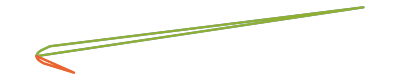

```mathematica
PolarPlot[Evaluate[Flatten[{eq+3,eq-3}]/.Subscript[ρ, 0]->-2],{θ,0,2Pi},PlotLegends->"Expressions",Axes->False]
```